```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.1,Jtwo,0.1,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.8850612031567836}]
```

{z→0.885061}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.1,l->0.1}
```

0.885061+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.8850612031567836]]
```

{{0.005,0.889544},{0.01,0.89375},{0.015,0.897612},{0.02,0.901046},{0.025,0.903955},{0.03,0.906238},{0.035,0.907803},{0.04,0.908589},{0.045,0.908581},{0.05,0.907813},{0.055,0.906353},{0.06,0.904289},{0.065,0.901709},{0.07,0.898695},{0.075,0.895317},{0.08,0.891634},{0.085,0.887691},{0.09,0.883526},{0.095,0.879171},{0.1,0.874648}}

```mathematica
moduler[Lister[-1,-0.005,0.8850612031567836]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.35868 and 3.20641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.35868 and 3.20641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {3.10858279330015}. NIntegrate obtained 0.294377 and 3.20015 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{-0.005,0.880353},{-0.01,0.87546},{-0.015,0.870413},{-0.02,0.865234},{-0.025,0.859941},{-0.03,0.854548},{-0.035,0.854548},{-0.04,0.854582},{-0.045,0.854606},{-0.05,0.854675},{-0.055,0.854685},{-0.06,0.854717},{-0.065,0.854794},{-0.07,0.854865},{-0.075,0.854964},{-0.08,0.855223},{-0.085,0.85526},{-0.09,0.855282},{-0.095,0.85528},{-0.1,0.855284}}

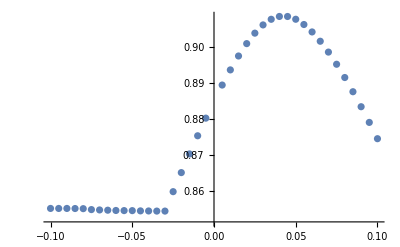

```mathematica
ListPlot[{{0.005,0.8895443042880239},{0.01,0.8937501862371299},{0.015,0.8976117128589126},{0.02,0.9010457144558033},{0.025,0.903955250381945},{0.03,0.9062380977141129},{0.035,0.907802760125975},{0.04,0.9085885425445578},{0.045,0.9085807669011964},{0.05,0.9078125774167529},{0.055,0.9063529689145311},{0.06,0.9042887771715518},{0.065,0.901709009606694},{0.07,0.8986952190561132},{0.075,0.895317422521333},{0.08,0.8916335381054745},{0.085,0.8876905267173224},{0.09,0.8835261100279289},{0.095,0.8791705011213276},{0.1,0.874647922175772},{-0.005,0.8803532018936951},{-0.01,0.8754603288389791},{-0.015,0.8704129712336262},{-0.02,0.8652341653660836},{-0.025,0.8599414128474069},{-0.03,0.8545480611725725},{-0.035,0.8545482596869279},{-0.04,0.8545815317610315},{-0.045,0.8546056873212434},{-0.05,0.8546745140351266},{-0.055,0.8546845687422258},{-0.06,0.8547165984046659},{-0.065,0.8547941187733309},{-0.07,0.8548650931966241},{-0.075,0.8549636758211723},{-0.08,0.8552226584505126},{-0.085,0.8552600752380071},{-0.09,0.8552815060599943},{-0.095,0.8552800500497934},{-0.1,0.8552836611042015}}]
```

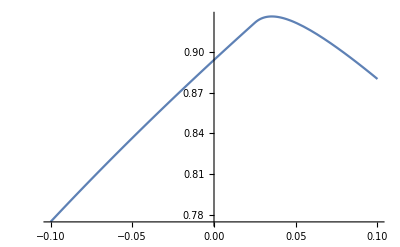

```mathematica
Plot[Sqrt[1+2(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1}]
```